## Import astro

/Users/cmccabe/Google Drive/DarkSphere/AtomicCalcs/Plots/Scattering/Xenon

/Users/cmccabe

InterpolatingFunction[…]

2.62585×10^-10

0.

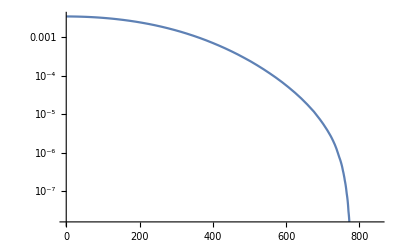

```mathematica
SetDirectory[NotebookDirectory[]]
Lgvmin=Import["gvmin_round.dat"];
ResetDirectory[]
fgvmin=Interpolation[Lgvmin,InterpolationOrder->1]
fgvmin[779]
fgvmin[780]

LogPlot[fgvmin[vmin],{vmin,0,850}]
```

## Import fion

/Users/chris/Downloads/molDM-main/Xenon/Formfactor_HX

/Users/chris

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«2 more identical outputs»

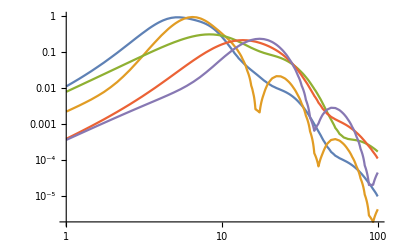

```mathematica
(*set path to form factor files*)
SetDirectory[NotebookDirectory[]<>"../Formfactor_HX"]
(*set path to form factor files*)

L4s=Import["Xe4s_Sch_grid.dat"];
L4p=Import["Xe4p_Sch_grid.dat"];
L4d=Import["Xe4d_Sch_grid.dat"];
L5s=Import["Xe5s_Sch_grid.dat"];
L5p=Import["Xe5p_Sch_grid.dat"];
ResetDirectory[]

f4s=Interpolation[L4s,InterpolationOrder->1]
f4p=Interpolation[L4p,InterpolationOrder->1]
f4d=Interpolation[L4d,InterpolationOrder->1]
f5s=Interpolation[L5s,InterpolationOrder->1]
f5p=Interpolation[L5p,InterpolationOrder->1]

LogLogPlot[{f5p[qx,0.02],f5s[qx,0.02],f4d[qx,0.02],f4p[qx,0.02],f4s[qx,0.02]},{qx,1,100}]
```

## Parameters

```mathematica
Params4s=Association[
wnl->2,
Inl->213.2,
fionnl->f4s
];

Params4p=Association[
wnl->6,
Inl->146.1,
fionnl->f4p
];

Params4d=Association[
wnl->10,
Inl->68.5,
fionnl->f4d
];

Params5s=Association[
wnl->2,
Inl->23.3,
fionnl->f5s
];

Params5p=Association[
wnl->6,
Inl->12.7,
fionnl->f5p
];
```

## Rate calculation: FDM = 1

σe40 is the cross section relative to 10^-40 cm^2

#### dR/dE calculation: FDM = 1

```mathematica
TdRdE[mDMMeV0_,MNGeV0_,σe40_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

ρ=0.3;(*GeV cm^-3*)
σe=10^-40 σe40a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=779;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=  ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM=1

```mathematica
TdRETotal[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ4s=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params4s],InterpolationOrder->1];
fσ4p=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params4p],InterpolationOrder->1];
fσ4d=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params4d],InterpolationOrder->1];
fσ5s=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params5s],InterpolationOrder->1];
fσ5p=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params5p],InterpolationOrder->1];

Ftot[x_]:=fσ5p[x]+fσ5s[x]+fσ4d[x]+fσ4p[x]+fσ4s[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
AXe=131.29;
MNGeV=AXe .931494; (*GeV*)
σ1=1; (*10^-40cm^2 cross section*)

TR30MeV=TdRETotal[30,MNGeV,σ1];
TR300MeV=TdRETotal[300,MNGeV,σ1];
TR1000MeV=TdRETotal[1000,MNGeV,σ1];

SetDirectory[NotebookDirectory[]];
Export["dRdE_Xe_30MeV.dat",TR30MeV]
Export["dRdE_Xe_300MeV.dat",TR300MeV]
Export["dRdE_Xe_1000MeV.dat",TR1000MeV]
ResetDirectory[];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {47.263}. NIntegrate obtained 0.0319145 and 1.49261×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {47.2858}. NIntegrate obtained 0.0325244 and 9.9553×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {50.1987}. NIntegrate obtained 0.0331699 and 1.55801×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {198.136}. NIntegrate obtained 0.00332914 and 1.99496×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {198.153}. NIntegrate obtained 0.00332843 and 1.94924×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {198.171}. NIntegrate obtained 0.00332813 and 2.01763×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {199.339}. NIntegrate obtained 0.0022869 and 3.1158×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {199.356}. NIntegrate obtained 0.0022862 and 3.44666×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {199.375}. NIntegrate obtained 0.00228577 and 3.6492×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dRdE_Xe_30MeV.dat

dRdE_Xe_300MeV.dat

dRdE_Xe_1000MeV.dat

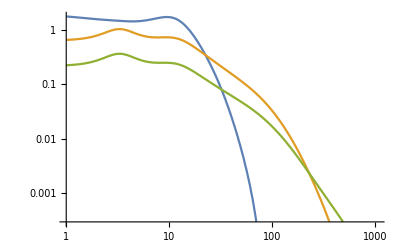

```mathematica
(*convert x-axis to eV*)
TR30MeV[[All,1]]=10^3 TR30MeV[[All,1]];
TR300MeV[[All,1]]=10^3 TR300MeV[[All,1]];
TR1000MeV[[All,1]]=10^3 TR1000MeV[[All,1]];


Show[ListLogLogPlot[{TR30MeV,TR300MeV,TR1000MeV},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```

## Rate calculation: FDM = (alpha me / q)^2

σe37 is the cross section relative to 10^-37 cm^2

#### dR/dE calculation: FDM = (alpha me / q)^2

```mathematica
TdRdElightmed[mDMMeV0_,MNGeV0_,σe37_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

αEM=1/137.04;
ρ=0.3;(*GeV cm^-3*)
σe=10^-37 σe37a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
mekeV=1000. meMeV;(*keV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=779;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

FDM[qkeV_]:=(αEM mekeV/qkeV)^2;

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=   FDM[qkeV]^2ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM = (alpha me / q)^2

```mathematica
TdRETotallightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ4s=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params4s],InterpolationOrder->1];
fσ4p=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params4p],InterpolationOrder->1];
fσ4d=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params4d],InterpolationOrder->1];
fσ5s=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params5s],InterpolationOrder->1];
fσ5p=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params5p],InterpolationOrder->1];

Ftot[x_]:=fσ5p[x]+fσ5s[x]+fσ4d[x]+fσ4p[x]+fσ4s[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
AXe=131.29;
MNGeV=AXe .931494; (*GeV*)
σ1=1; (*10^-37cm^2 cross section*)

TR30MeVlightmed=TdRETotallightmed[30,MNGeV,σ1];
TR300MeVlightmed=TdRETotallightmed[300,MNGeV,σ1];
TR1000MeVlightmed=TdRETotallightmed[1000,MNGeV,σ1];

SetDirectory[NotebookDirectory[]];
Export["dRdE_Xe_30MeV_lightmed.dat",TR30MeVlightmed]
Export["dRdE_Xe_300MeV_lightmed.dat",TR300MeVlightmed]
Export["dRdE_Xe_1000MeV_lightmed.dat",TR1000MeVlightmed]
ResetDirectory[];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {36.4570405118709}. NIntegrate obtained 0.000827353 and 4.87158×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {35.9886480467386}. NIntegrate obtained 0.000850311 and 5.03725×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {36.5202733424678}. NIntegrate obtained 0.000874401 and 6.35632×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {113.236359047072}. NIntegrate obtained 8.05457×10^-7 and 2.80269×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {198.153}. NIntegrate obtained 8.06574×10^-7 and 2.83813×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {198.171}. NIntegrate obtained 8.07889×10^-7 and 2.9284×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {130.3497904294694080817862413823604583740234375}. NIntegrate obtained 4.58419×10^-7 and 8.67318×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {130.36819861030598843854022561572492122650146484375}. NIntegrate obtained 4.59165×10^-7 and 8.48946×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {130.3874744892414554442439111880958080291748046875}. NIntegrate obtained 4.60032×10^-7 and 8.28645×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dRdE_Xe_30MeV_lightmed.dat

dRdE_Xe_300MeV_lightmed.dat

dRdE_Xe_1000MeV_lightmed.dat

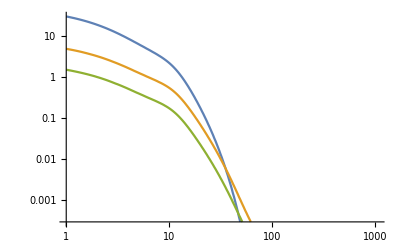

```mathematica
(*convert x-axis to eV*)
TR30MeVlightmed[[All,1]]=10^3 TR30MeVlightmed[[All,1]];
TR300MeVlightmed[[All,1]]=10^3 TR300MeVlightmed[[All,1]];
TR1000MeVlightmed[[All,1]]=10^3 TR1000MeVlightmed[[All,1]];


Show[ListLogLogPlot[{TR30MeVlightmed,TR300MeVlightmed,TR1000MeVlightmed},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```